```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
j1=(1-8 m u^2-24 u^3+16 m^2 u^4)^3/(u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4));
```

```mathematica
FullSimplify[Together[j1-1728]]
```

((1-4 u^2 (3 m+9 u-12 m^2 u^2-36 m u^3+2 (-27+8 m^3) u^4))^2)/(u^8 (m+u-8 m^2 u^2-36 m u^3+(-27+16 m^3) u^4))

```mathematica
Factor[Together[j1-((27+256 m^3) (243+256 m^3)^3)/(16777216 m^9)]]
```

-(((8 m+9 u)^2 (-262144 m^7+589824 m^6 u-995328 m^5 u^2+6291456 m^8 u^2+1492992 m^4 u^3+4718592 m^7 u^3-2099520 m^3 u^4-18579456 m^6 u^4-62914560 m^9 u^4+2834352 m^2 u^5+35831808 m^5 u^5-160432128 m^8 u^5-3720087 m u^6-57106944 m^4 u^6-12386304 m^7 u^6+335544320 m^10 u^6+4782969 u^7+83140992 m^3 u^7+230916096 m^6 u^7+1056964608 m^9 u^7-38263752 m^2 u^8-302330880 m^5 u^8+1019215872 m^8 u^8-939524096 m^11 u^8+57395628 m u^9+589545216 m^4 u^9+191102976 m^7 u^9-2650800128 m^10 u^9-129140163 u^10-1556059248 m^3 u^10-3332358144 m^6 u^10-1679818752 m^9 u^10+1073741824 m^12 u^10))/(16777216 m^9 u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4)))

```mathematica
Simplify[Discriminant[Numerator[j1]-j Denominator[j1],u]]
```

(-1728+j)^6 j^8 (27+256 m^3)^3 (-387420489-4897760256 m^3-12899450880 m^6+16777216 (-756+j) m^9-4294967296 m^12)

```mathematica
Series[-387420489-4897760256 m^3-12899450880 m^6+16777216 (-756+j) m^9-4294967296 m^12,{j,0,100}]
```

-(27+256 m^3) (243+256 m^3)^3+16777216 m^9 j+O[j]^101

```mathematica
Solve[-(27+256 m^3) (243+256 m^3)^3+16777216 m^9 j==0,j]
```

{{j→((27+256 m^3) (243+256 m^3)^3)/(16777216 m^9)}}

```mathematica
FactorInteger[1073741824]
```

{{2,30}}

```mathematica
Simplify[x/.Solve[x^2(x+10)-eps==0,x]]
Simplify[Series[%, {eps,0,2}]]
```

{1/3 (-10+100/(-1000+(27 eps)/2+3/2 √3 √(eps (-4000+27 eps)))^(1/3)+(-1000+(27 eps)/2+3/2 √3 √(eps (-4000+27 eps)))^(1/3)),1/12 (-40-(200 (1+ⅈ √3))/(-1000+(27 eps)/2+3/2 √3 √(eps (-4000+27 eps)))^(1/3)+ⅈ 2^(2/3) (ⅈ+√3) (-2000+27 eps+3 √3 √(eps (-4000+27 eps)))^(1/3)),1/12 (-40+(200 ⅈ (ⅈ+√3))/(-1000+(27 eps)/2+3/2 √3 √(eps (-4000+27 eps)))^(1/3)-2^(2/3) (1+ⅈ √3) (-2000+27 eps+3 √3 √(eps (-4000+27 eps)))^(1/3))}

{Piecewise[{{(ⅈ √eps √eps)/(√10 √-eps)-eps/200+(ⅈ √eps eps^(3/2))/(1600 √10 √-eps)-eps^2/100000+O[eps]^(5/2), Im[30 √30 √-eps+81/80 √(3/10) (-eps)^(3/2)+(27 eps)/2]≥0}, {(ⅈ √-eps √eps)/(√10 √eps)-eps/200+(ⅈ √-eps eps^(3/2))/(1600 √10 √eps)-eps^2/100000+O[eps]^(5/2), True}}],Piecewise[{{(ⅈ √eps √eps)/(√10 √-eps)-eps/200+(ⅈ √eps eps^(3/2))/(1600 √10 √-eps)-eps^2/100000+O[eps]^(5/2), Im[60 √30 √-eps+81/40 √(3/10) (-eps)^(3/2)+27 eps]<0&&Im[30 √30 √-eps+81/80 √(3/10) (-eps)^(3/2)+(27 eps)/2]<0}, {-10+eps/100+eps^2/50000+O[eps]^(5/2), True}}],Piecewise[{{(ⅈ √-eps √eps)/(√10 √eps)-eps/200+(ⅈ √-eps eps^(3/2))/(1600 √10 √eps)-eps^2/100000+O[eps]^(5/2), Im[60 √30 √-eps+81/40 √(3/10) (-eps)^(3/2)+27 eps]≥0&&Im[30 √30 √-eps+81/80 √(3/10) (-eps)^(3/2)+(27 eps)/2]≥0}, {-10+eps/100+eps^2/50000+O[eps]^(5/2), True}}]}

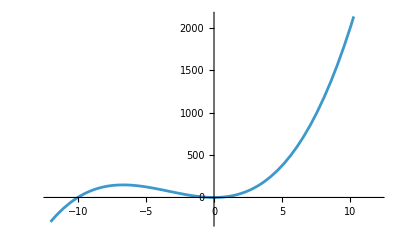

```mathematica
Plot[x^2(x+10),{x,-12,12}]
```

```mathematica
delt=u^8 (m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4)/.{u->u l^(1/3),m->l^(1/3)}//Simplify
```

l^3 u^8 (1+u-8 l u^2-36 l u^3+l (-27+16 l) u^4)

```mathematica
uroots=Simplify[u/.Solve[u^8 (8+9 u)^2 (64-80 u+153 u^2)==0,u]]//DeleteDuplicates//SortBy[#, Abs]&
```

{0,-8/9,8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2)}

```mathematica
Simplify[delt/.{l->-27/256}]
Simplify[Series[%, {u,uroots[[3]],3}]]
```

-(19683 u^8 (8+9 u)^2 (64-80 u+153 u^2))/68719476736

(8 √2 (5 ⅈ+8 √2)^8 (89 ⅈ+88 √2) (u-8/153 (5-8 ⅈ √2)))/4408978660281963-(((5 ⅈ+8 √2)^7 (-26947 ⅈ+12400 √2)) (u-8/153 (5-8 ⅈ √2))^2)/461069663820336-(7 ⅈ (5 ⅈ+8 √2)^6 (-16659 ⅈ+6856 √2) (u-8/153 (5-8 ⅈ √2))^3)/24108217716096+O[u-8/153 (5-8 ⅈ √2)]^4

```mathematica
(* ord(delt) *)
```

```mathematica
{g2,g3}=Simplify[{MirrorCurveg2[l^(1/3),u l^(1/3)], MirrorCurveg3[l^(1/3),u l^(1/3)]}]
```

{27 (1+16 l^2 u^4-8 l u^2 (1+3 u)),27 (-1+64 l^3 u^6+12 l u^2 (1+3 u)-24 l^2 u^4 (2+6 u+9 u^2))}

```mathematica
Simplify[{g2,g3}/.{l->-27/256}]
Simplify[Series[%, {u,uroots[[3]],3}]]
```

{27 (1+(729 u^4)/4096+27/32 u^2 (1+3 u)),27 (-1-(19683 u^6)/262144-81/64 u^2 (1+3 u)-(2187 u^4 (2+6 u+9 u^2))/8192)}

{(864 (287-24 ⅈ √2))/83521-(108 ⅈ (-2309 ⅈ+2854 √2) (u-8/153 (5-8 ⅈ √2)))/4913+(729 (433-584 ⅈ √2) (u-8/153 (5-8 ⅈ √2))^2)/4624+(2187 (73-8 ⅈ √2) (u-8/153 (5-8 ⅈ √2))^3)/2176+O[u-8/153 (5-8 ⅈ √2)]^4,(3456 (6840-863 ⅈ √2))/24137569+(54 (1247063+1315864 ⅈ √2) (u-8/153 (5-8 ⅈ √2)))/1419857+(243 (102269-6224 ⅈ √2) (u-8/153 (5-8 ⅈ √2))^2)/668168+(2187 (24983+2704 ⅈ √2) (u-8/153 (5-8 ⅈ √2))^3)/157216+O[u-8/153 (5-8 ⅈ √2)]^4}

```mathematica
Simplify[Simplify[MirrorCurveJ[l^(1/3),u l^(1/3)]]/.{l->-27/256}]
Series[%,{u,uroots[[2]],4}]
```

-((8+9 u) (512-576 u+1080 u^2+81 u^3)^3)/(19683 u^8 (64-80 u+153 u^2))

-27648 (u+8/9)-181872 (u+8/9)^2-2882817/4 (u+8/9)^3-568640925/256 (u+8/9)^4+O[u+8/9]^5

```mathematica
Graphics[{PointSize[.015],Point[ReIm/@uroots],

},
PlotRange->{{-1,1},{-1,1}}
]
```

-Graphics-